```mathematica
SetDirectory[NotebookDirectory[]];
Remove["Global`*"]//Quiet;
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"lib_v_3.nb"}],InsertResults->False];
```

# Teoria gier

## Proceduralne podejście do uczenia w grach

Populacja i stan populacji. Całość tego wykładu dotyczy jednie gier dwuosobowych symetrycznych. Podstawowa idea podejścia proceduralnego opiera się o pojedynczą populację graczy. Zakładamy, że istnieje duża ale skończona grupa graczy o liczności N, którą zazwyczaj nazywa się populacją. Stan populacji oznaczamy przez y^N, gdzie przez stan populacji rozumiemy wektor udziałów akcji w populacji. Wektor y jest zatem rozkładem prawdopodobieństwa ale ponieważ liczba graczy w populacji jest skończona więc musi on należeć do siatki na sympleksie. Poniżej są pokazane przykłady takiej siatki dla jednej populacji w grze z trzema akcjami.

```mathematica
Manipulate[
Show[{
Graphics3D[{Opacity[.5],Simplex[IdentityMatrix[3]]}],
Graphics3D[{PointSize[Medium],Point[Flatten[
Permutations/@IntegerPartitions[k,{3},Range[0,k]],
1
]/k]}]
}],
{k,3,20,1},SaveDefinitions->True]
```

Ewolucja stanu populacji. Ewolucja stanu populacji odbywa się w czasie dyskretnym. Niech δ>0 będzie czasem pojedynczego kroku, czas zawiera się w zbiorze t=0, δ,2δ,3δ,… Zakładamy, że procedura ewolucji przebiega standardowo dla modeli ewolucyjnych. W każdej jednostce czasu, losowo wybranych gracz może zmienić swoją akcję. Podstawy takiej zmiany zależą od modelu, np. gracz może obserwować wybraną losowo grupę i na tej podstawie wybrać swoją akcję, gracz może zagrać w grę z losowo wybranym graczem z populacji i na tej podstawie wybrać swoją akcję, itd.

Ponieważ w każdej chwili czasu tylko jeden gracz może zmienić swoją akcję (model asynchroniczny)  a więc stan populacji pomiędzy kolejnymi czasam może się różnić tylko na dwóch miejscach, na jednym będzie mniejszy  o 1/N i na jednym będzie większy o 1/N. Zgodnie z tym określamy prawdopodobieństwo, zmiany akcji przez jednego gracza z akcji o numerze k na akcję o numerze j w następujący sposób

p_(k j)(y^N)=Pr(y^N(t+δ)=y^N(t)+(e_j-e_k)/N|y^N(t)=y^N).

Dla prostoty zakładamy, że δ=1/N co daje

p_(k j)(y^N)=Pr(y^N(t+1/N)=y^N(t)+(e_j-e_k)/N|y^N(t)=y^N).

Zakładamy, że funkcje p_(k j) są ciągłe na sympleksie oraz, że dla dowolnego y_k^N=0 zachodzi p_(k j)=0, a więc jeżeli żaden gracz w populacji nie gra akcji o numerze k to prawdodobieństwo, że w takim stanie populacji jednej gracz porzuci taką akcję na rzecz innej akcji jest oczywiście zerowe.

Uwaga. Warto zauważyć, że podane wyżej prawdopodobieństwa przejścia są całkowitymi prawdopodobieństwa przejścia dla całego systemu. Jeżeli określimy warunkowe prawdopodobieństwa wyboru danej akcji (na poziomie gracza) to oczywiście trzeba to prawdopodobieństwo przemnożyć przez prawdodpodobieństwo, że gracz o zadanej strategii zostanie wylosowany. Przykładowo, jeżeli (p̃)_(k j) jest warunkowym prawdopodobieństwem wyboru akcji j pod warunkiem, że gracz obecnie wykorzystuje akcję k, to prawdopodobieństwo zmiany systemy wynosi wtedy y_k^N ·(p̃)_(k j)(y^N).

Uwaga. W powyższy sposób został określony łańcych Markowa na pewnej siatce stanów na sympleksie. Każdy taki stan interpretujemy jako strategię mieszaną. W zależości od definicji warunkowego prawdopodobieństwa przejścia będzie otrzymywali różne modele uczenia. Warto zauważyć, że w powyższym modelu można uzależnić prawdopodobieństwo wyboru danego gracza od stanu populacji ale w tym wykładzie nie będziemy się tym zajmowali.

## Przykłady

### Prosty model wpływu większości

Zakładamy, że mamy tylko dwie akcje: a i b. Kolejność tych akcji nie ma żadnego znaczenia. Możemy o nich myśleć jak o markach albo rozwiązaniach technologicznych. Procedura podejmowania decyzji każdego gracza w populacji wygląda w następujący sposób:
- sprawdź udział akcji w populacji
- wybierz swoją akcję z prawdopodobieństwem równym udziałowi dla danej akcji.

Dla takiego prostego modelu dopasowywania technologii albo wpływu większości możemy łatwo zdefiniować łańcuch Markowa odpowiadający modelowi. W poniższym łańcuchu

```mathematica
n=20; (* wielkość populacji *)
```

```mathematica
states=Range[0,n]/n; (* stany, w których może znajdować się populacja *)
```

```mathematica
dict=Thread[Range[1,n+1]->states];
```

```mathematica
p[x_,sTo_,n_]:=Module[{ret=0},
If[sTo-x==1/n,ret=(1-x)x];
If[x-sTo==1/n,ret=x (1-x)];
If[x==sTo,ret=1-Sign[x] x (1-x) -Sign[1-x] x (1-x)];
ret
]
```

```mathematica
transMatrix=Outer[(p[#1,#2,n])&,states,states];
```

```mathematica
𝒫=DiscreteMarkovProcess[
IdentityMatrix[n+1]⟦Floor[n/2]+1⟧,
transMatrix
];
```

Mając zdefiniowany łańcuch Markowa możemy zadań np. pytanie o rozkład graniczny.

```mathematica
limitingDist =StationaryDistribution[𝒫];
```

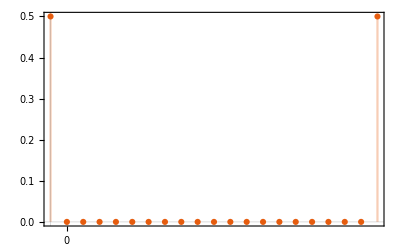

```mathematica
DiscretePlot[
PDF[limitingDist,k+1],
{k,0,n,1},
PlotTheme->"Scientific",
FrameTicks->{{Automatic,None},{{{1,0},{n+1,1}},None}}
]
```

Nie jest to zaskakujące bo oczywiście mamy dwa stany pochłaniające, w których albo jedna albo druga technologia wygrywa.

```mathematica
MarkovProcessProperties[𝒫,"AbsorbingClasses"]/.dict
```

{{0},{1}}

Znacznie ciekawe pytanie to ile czasu jest konieczne aby wygrała np. pierwsza technologia (technologia a). Typowe zachowanie się scieżek w takim modelu jest pokazane poniżej.

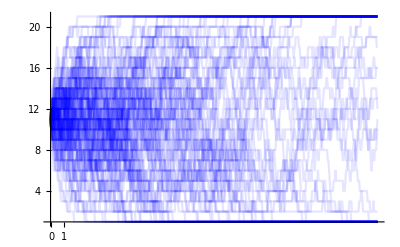

```mathematica
ListPlot[
RandomFunction[𝒫,{0,500},100],
PlotRange->{1,n+1},
Joined->True,
PlotStyle->Directive[Blue,Opacity[.1]],
Ticks->{{{1,0},{n+1,1}},Automatic},
PlotRange->All
]
```

```mathematica
timeToWinFirstBrand=FirstPassageTimeDistribution[𝒫,n+1];
```

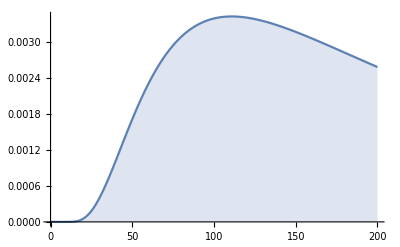

```mathematica
DiscretePlot[PDF[timeToWinFirstBrand,k],{k,0,200},PlotRange->All]
```

Średnio zajmuje to następującą liczbę kroków.

```mathematica
Mean[timeToWinFirstBrand]//N
```

267.509

Odchylenie standardowe wynosi jak poniżej.

```mathematica
StandardDeviation[timeToWinFirstBrand]//N
```

202.76

Ile średnio czasu zajmuje aby jedna z marek wygrała?

```mathematica
timeToWinAnyBrand=FirstPassageTimeDistribution[𝒫,{1,n+1}];
```

```mathematica
Mean[timeToWinAnyBrand]//N
```

267.509

```mathematica
StandardDeviation[timeToWinAnyBrand]//N
```

202.76

Warto zauważyć, że w tym modelu nie występuje w ogóle macierz wypłat. Wynika to z zastosowanej procedury podejmowania decyzji w kontekście wyboru akcji.

### Prosty model wyboru najlepszej odpowiedzi

Podobnie jak poprzednio zakładamy skończoną populację ale tym razem procedura podejmowania decyzji jest oparta o grę dwuosobową symetryczną.

```mathematica
g1=<|"player 1"->IdentityMatrix[2],"player 2"->IdentityMatrix[2]|>;
MatrixForm/@g1
```

<|player 1→(1 | 0
0 | 1),player 2→(1 | 0
0 | 1)|>

```mathematica
g1=<|"player 1"->RotateLeft@IdentityMatrix[2],"player 2"->RotateLeft@IdentityMatrix[2]|>;
MatrixForm/@g1
```

<|player 1→(0 | 1
1 | 0),player 2→(0 | 1
1 | 0)|>

Procedura podejmowania decyzji dla wybranego gracza jest następująca:
- wybrany gracz otrzymuje informacje o stanie populacji (nie o tym co gra każdy gracz a jedynie statystykę)
- gracz wybiera tę akcję, która jest dana przez najlepszą odpowiedź a jeżeli jest to zbiór to wybiera z niego dowolną akcję ale z równymi prawdopodobieństwami.

```mathematica
n=10; (* wielkość populacji *)
```

```mathematica
states=Range[0,n]/n; (* stany, w których może znajdować się populacja *)
```

```mathematica
dict=Thread[Range[1,n+1]->states];
```

```mathematica
p[x_,sTo_,n_,g_]:=Module[{ret=0,br},
(* up *)
If[sTo-x==1/n,
br=bestReplyK[g,{{x,1-x},{x,1-x}},1];
If[Head[br]==Point,ret=(1-x) br⟦1⟧⟦1⟧];
If[Head[br]==Simplex,ret=(1-x)/2];
];
(* down *)
If[x-sTo==1/n,
br=bestReplyK[g,{{x,1-x},{x,1-x}},1];
If[Head[br]==Point,ret=x br⟦1⟧⟦2⟧];
If[Head[br]==Simplex,ret=x/2];
];
ret
]
```

```mathematica
transMatrix=Outer[(p[#1,#2,n,g1])&,states,states];
Table[transMatrix⟦k,k⟧=1-Total[transMatrix⟦k⟧],{k,1,n+1}]; (* normalizacja *)
```

```mathematica
𝒫=DiscreteMarkovProcess[
IdentityMatrix[n+1]⟦Floor[n/2]+1⟧,
transMatrix
];
```

Podobnie jak poprzednio możemy zadać pytanie związane z rozkładem granicznym (który nie zawsze jest stacjonarnym rozkładem).

```mathematica
limitingDist =StationaryDistribution[𝒫];
```

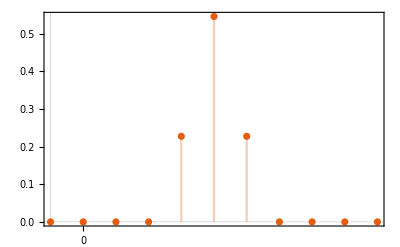

```mathematica
DiscretePlot[
PDF[limitingDist,k+1],
{k,0,n,1},
PlotTheme->"Scientific",
FrameTicks->{{Automatic,None},{{{1,0},{n+1,1}},None}}
]
```

```mathematica
MarkovProcessProperties[𝒫,"AbsorbingClasses"]/.dict
```

{}

Typowe zachowanie się populacji jest pokazane poniżej.

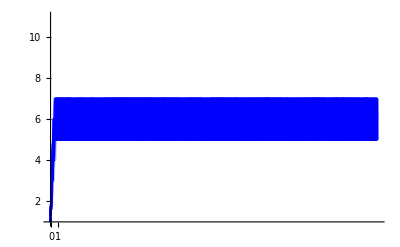

```mathematica
ListPlot[
RandomFunction[𝒫,{0,500},100],
PlotRange->{1,n+1},
Joined->True,
PlotStyle->Directive[Blue,Opacity[.1]],
Ticks->{{{1,0},{n+1,1}},Automatic},
PlotRange->{0,n}
]
```

Wniosek z powyższych modeli symulacyjnych jest taki, że trajektorie łańcucha Markowa “zbiegają” do niektórych równowag Nasha. Oczywiście należy zdefiniować ściśle pojęcie zbiegania.

## Przybliżenie przy pomocy równań różniczkowych

Aproksymacja. Analiza łańcucha Markowa jest jak najbardziej do zrobienia ale tylko dla relatywnie małych populacji, co nie jest specjalnie interesujące jeżeli weźmie się pod uwagę założenia modelu. W szczególności założenie anonimowości graczy i dobrego “wymieszania” popoulacji (well-mixed population) wymaga dużych populacji. Dla dużyć populacji wygodniej jest badać układ równań różniczkowych opisujących “średnie” zachowanie populacji. Układ równań ma następującą postać

(ⅆ y_k)/ⅆt=f_k(y)=∑_j p_(j k)(y)-∑_j p_(k j)

lub w postaci wektorowej ẏ=f(y). Warto zwrócić, że skalowanie czasu jest tutaj osiągnięte przez założenie, że δ N=1. Potok związany z powyższym równaniem oznaczamy przez ξ(t,y).

Uwaga. Powyższa dynamika jest polem wektorowym określonym na sympleksie (wystarczy zobaczyć, że dla dowolnego elementu sympleksu y zadany wektor jest prostopadły do wektora normalnego sympleksu. Dodatkowo, sympleks jest niezmienniczy wprzód dla powyższe dynamiki, co wynika z założenia y_k=0⇒p_(k j)(y)=0 (jeżeli nikt nie gra akcji k to nikt nie może zmienić akcji z k-tej na inną). A więc, jeżeli początkowy stan układu należy do sypleksu to orbita wprzód należy do sympleksu. Jest to więc poprawnie określona dynamika opisująca zachowanie stanu populacji w czasie. Warto również zauważyć, że całość modelowania jest tutaj sprowadzona do zdefiniowania prawdopodobieństw przejścia.

Notacja dla aproksymacji I. Dynamika populacji przybliża zachowanie się łańcucha Markowa w kilku znaczeniach. Pierwsze znaczenie polega na tym, że trajektorie układu populacyjnego pozostają blisko realizacji łańcucha Markowa. Definiujemy następujący ciągły proces stochastyczny

(ŷ)^N(t)=y^N(k δ)+(t- k δ)/δ(y^N((k+1) δ)-y^N(k δ)).

Jest to więc interpolacja liniowa procesu dyskretnego. Następnie definiujemy “odległość” pomiędzy trajektorią a realizacją jako

D^N(T,y)=max_(0≤t≤T) (‖(ŷ)^N(t)-ξ(t,y)‖)_∞.

Twierdzenie. Niech ϵ>0 oraz T>0 będą dowolne. Wtedy istnieje liczba c>0, taka, że dla dostatecznie dużego N zachodzi

Pr(D^N(T,x)≥ϵ|y^N(0)=x)≤2 N ⅇ^(-ϵ^2c N)

dla dowolnego y∈△.

Uwaga. Powyższe twierdzenie mówi tyle, że jeżeli tylko ustalimy zakresu czasu, to prawdopodobieństwo zdarzenia, że realizacja łańcucha Markowa odchyli się od trajektorii dynamiki populacyjnej o więcej niż ϵ wykładniczo maleje razem z wielkością populacji. A więc na skończonych, dowolnie długich, odcinkach czasu zachowanie dynamiki populacyjnej dowolnie dobrze przybliża zachowanie się łańcucha Markowa. Twierdzenie to nie oznacza, że asymptotycznie dynamika populacyjna ma coś wspólnego z łańcuchem Markowa.

Notacja dla aproksymacji II. Przez γ(y) oznaczamy orbitę dynamiki populacyjnej zawierającą punkt y. Przez γ^+(y) oznaczamy orbitę wprzód dla tej samej dynamiki zawierającą punkt y. Niech U⊂ℝ^n będzie zbiorem borelowskim oraz niech (ŷ)^N(0)∈U. Przez czas wyjścia rozumiemy zmienną losową zdefiniowaną jako

τ^N(U)=inf {t≥0:(ŷ)^N(t)∉U}.

Twierdzenie. Niech U⊂ℝ^n będzie zbiorem otwartym, cl(γ^+(y))∈U oraz (ŷ)^N(0)→y przy N→∞. Wtedy zachodzi

Pr(lim_(N→∞) τ^N(U)=∞)=1.

Uwaga. Powyższe twierdzenie oznacza, że jeżeli tylko łańcuch Markowa wystartuje z tego samego warunku początkowego co trajektora dynamiki popoulacyjnej to pozostanie w otoczeniu domknięcia trajektorii wprzód dowolnegi długo z prawdopodobieństwem 1. Z powyższego twierdzenia można pokazać dwa wnioski.

Wniosek. Niech A będzie atraktorem dla dynamiki populacyjnej oraz niech V⊂B(A), gdzie B(A) jest basenem przyciągania atraktora A i V jest dowolnym otoczeniem atraktora A. Wted istnieje otoczenie U⊂V atraktora A, takie, że cl(U)⊂B(A) oraz

Pr((lim inf)_(N→∞) τ^N(U)=∞)=1

jeżeli (ŷ)^N(0)∈U.

Uwaga. Powyższy wniosek mówi, że jeżeli tylko łańcuch Markowa wystartuje dowolnie blisko atraktora, to z prawdodpobieństwem 1 pozostanie tam dowolnie długo. Podobny wniosek można sformułować dla niestabilnych zbiorów niezmienniczych ale nie jest on dla nas konieczny.

## Replikator

Replikator. Korzystając z odpowiedniej procedury podejmowania decyzji można dojść do równań replikatora, które dla gier symmetrycznych dwuosobowych są  następującej postaci

(ⅆ x_k)/ⅆt=u(e^k-x,x)·x_k, k=1,…,n,

gdzie x to stan populacji a u to funkcja wypłaty.

Powyższe równania można również zapisać w następującej postaci

(ⅆ x_k)/ⅆt=x_k (e^k·U·x-x·U·x).

Warto zauważyć związek prawej strony powyższej dynamiki z charakteryzacją równowagi Nasha, która była wykorzystywana w poprzednim wykładzie.

Dodatkowo, dodatnie tansformacje affinicze wypłat nie mają wpływu na dynamikę replikatora (poza przeskalowaniem czasu).

Notacja. Przez △ oznaczamy sympleks odpowiedni dla gry, która jest rózważana. Przez △^NE oznaczamy zbiór symetrycznych równowag Nasha. Przez △^o oznaczamy zbiór punktów stacjonarnych dynamiki replikatora. Niech △^(o o)=△^o∩int(△) oznacza zbiór punktów stacjonarnych znajdujących się we wnętrzu sympleksu.

Twierdzenie. Niech x_0∈int(△) oraz niech akcja k będzie ściśle zdominowana. Wtedy ξ_k(t,x_0)→0. Podobnie, jeżeli akcja k jest usuwana w procesie iteracyjnego usuwania akcji ściśle zdominowanych, to zachodzi ta sama teza.

Uwaga. Powyższe twierdzenie mówi, że jeżeli tylko początkowy stan układu należy do wnętrze (relatywnego) sympleksu to żadna strategia ścieśle zdominowana (bezpośrednio lub pośrednio) nie przetrwa pod dynamiką replikatora.

Twierdzenie. Zachodzą następujące zależności
(1) {e^1,…,e^n}∪△^NE⊂△^o,
(2) △^(o o)=△^NE∩int(△), 
(3) zbiór △^(o o) jest wypukły.

Uwaga. Powyższe twierdzenie mówi, że jeżeli tylko znajdziemy punkt stacjonarny dynamiki replikatora, który znajduje się wewnątrz sympleksu to automatycznie znajdziemy symetryczną równowagę Nasha. To prowadzi do prostego algorytmu znajdowania niektórych równowag Nasha w grach symetrycznych, który opiera się o rozwiązywanie numeryczne równań różniczkowych. Rozumowanie to można nieco rozszerzyć co daje poniższe twierdzenie.

Twierdzenie. Niech x_0∈int(△). Jeżeli ξ(t,x_0)→x to x∈△^NE.

Uwaga. Powyższe twierdzenie dokładniej precyzuje potencjalny algorytm. Wybieramy dany punkt początkowy i rozwiązujemy numerycznie dynamikę replikatora. Jeżeli rozwiązanie zbiega do jakiegoś punktu, to wiemy, że jest to równowaga Nasha. Takie podejście ma kilka problemów ale potencjalnie może dać nam jakieś równowagi Nasha (potencjalnie wszystkie asymptotycznie stabilne równowagi). Pozostaną równowagi, które nie są asymptotycznie stabilne (z których źródła można znaleźć odwracając czas ale równowagi stabilne w sensie Lapunowa i np. siodła nie dają się łatwo znaleźć tą metodą).

## Algorytm

### Funkcja

Algorytm. Zaproponowany algorytm wygląda w następujący sposób: wybierz losowy punkt z sympleksu, oblicz trajektorię startującą z wybranego punktu, zdecyduj czy trajektora ta zbiega, jeżeli zbiega to jej granica jest przybliżeniem symetrycznej równowagi Nasha. Poniższa funkcja automatyzuje w pewnym zakresie powyższ algorytm.

```mathematica
Format[x[s_]]:=Subscript[Style[x,Blue], s]
```

```mathematica
ClearAll[findSymmetricNashEquilibriaInSymmetricGameReplicator]
Options[findSymmetricNashEquilibriaInSymmetricGameReplicator]={timeSpan->10};
findSymmetricNashEquilibriaInSymmetricGameReplicator[g_,var_,OptionsPattern[]]:=Module[{v,vProjected,n,k,projection,f,fProjected,reg,p,initialConds,eqs,subs,sol,t},
n=Length[g["player 1"]];
v=Table[var[k],{k,1,n}];
vProjected=Most[v];
projection=Last[v]->1-Total[Most[v]];
f=Table[v⟦k⟧ (getPayoff[g,{IdentityMatrix[n]⟦k⟧,v}]⟦1⟧-getPayoff[g,{v,v}]⟦1⟧),{k,1,n}];
fProjected=Most[f/.projection];
reg=ConvexHullMesh[Most/@IdentityMatrix[n]];
(* losowanie punktu *)
p=RandomPoint[reg];
(* tworzenie warunków początkowych *)
initialConds=Table[vProjected⟦k⟧[0]==p⟦k⟧,{k,1,n-1}];
(* tworzenie podstawień *)
subs=Table[vProjected⟦k⟧->vProjected⟦k⟧[t],{k,1,n-1}];
(* tworzenie równań różniczkowych *)
eqs=Table[vProjected⟦k⟧'[t]==(fProjected⟦k⟧/.subs),{k,1,n-1}];
(* rozwiązywanie równania różniczkowego *)
sol=NDSolveValue[Join[eqs,initialConds],vProjected,{t,0,OptionValue[timeSpan]}];
<|
"region"->reg,
"full f"->f,
"full vars" -> v,
"projected f"->fProjected,
"projected vars"->vProjected,
"vars projection"->projection,
"time span"->OptionValue[timeSpan],
"initial state"->p,
"solution"->sol
|>
]
```

### Przykład (dwie akcje)

Definiujemy prostą dwuosobową grę symetryczną z dwoma strategiami.

```mathematica
g1=generateRandomSymmetricBimatrixGame[BinomialDistribution[15,1/2],2];
MatrixForm/@g1
```

<|player 1→(7 | 5
4 | 7),player 2→(7 | 4
5 | 7)|>

Dla powyższej gry możemy wykorzystać metody zdefiniowane wcześniej.

```mathematica
ne1=DeleteDuplicates[Round[findSymmetricNashEquilibriaInSymmetricGame[g1,50,x]["nash"],0.001]]
```

{{0.,1.},{0.4,0.6},{1.,0.}}

Następnie możemy porównać zachowanie się równań różniczkowych dla wielu pumktów początkowych.

```mathematica
sols=Table[
findSymmetricNashEquilibriaInSymmetricGameReplicator[g1,x],
{j,1,20}];
```

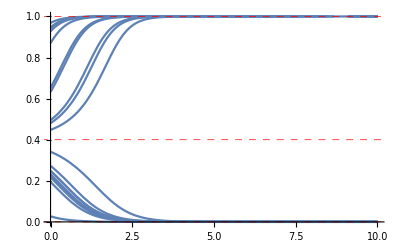

```mathematica
Show[
Plot[#["solution"]⟦1⟧[t],{t,0,#["time span"]},PlotRange->{0,1},GridLines->{None,First/@ne1},GridLinesStyle->Directive[Red, Dashed]]&/@sols
]
```

Jak widać rozwiązania zbiegają do pewnych równowag Nasha (stabilnych asymptotycznie) co nie daje wszystkich równowag Nasha ale można argumentować, że te równowagi, które nie są stabilne i tak nie będą obserwowane w rzeczywistości (pod warunkiem, że rzeczywistość jest dobrze opisana taką dynamiką). Mając obliczone rozwiązania możemy pozykać ich wartości dla największego uwzględnionego czasu.

```mathematica
DeleteDuplicates[({#,1-#})&/@Round[(#["solution"]⟦1⟧[#["time span"]])&/@sols,0.01]]
```

{{1.,0.},{0.,1.}}

### Przykład (trzy akcje)

Podobnie jak powyżej definiujemy przykładową grę.

```mathematica
g1=generateRandomSymmetricBimatrixGame[BinomialDistribution[15,1/2],3];
MatrixForm/@g1
```

<|player 1→(4 | 8 | 6
8 | 7 | 7
6 | 8 | 2),player 2→(4 | 8 | 6
8 | 7 | 8
6 | 7 | 2)|>

W następnej kolejności obliczamy równowagi Nash.

```mathematica
ne1=Sort@DeleteDuplicates[Round[findSymmetricNashEquilibriaInSymmetricGame[g1,50,x]["nash"],0.001]]
```

{{0.167,0.75,0.083}}

Porównujemy powyższe rozwiązania z rozwiązaniami pozyskanymi z podejścia ewolucyjnego.

```mathematica
sols=Table[
findSymmetricNashEquilibriaInSymmetricGameReplicator[g1,x,timeSpan->100],
{j,1,50}];
```

Możemy relatywnie łatwo wizualizować rozwiązania.

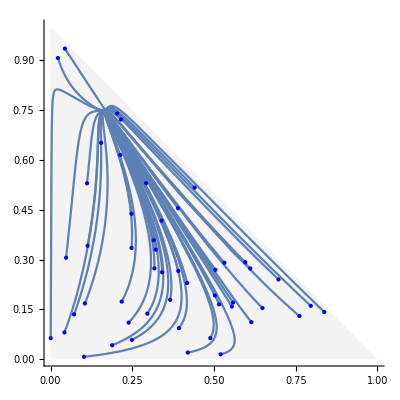

```mathematica
Show[{
Graphics[{Opacity[.3],LightGray,sols⟦1⟧["region"]}],
ParametricPlot[Through[#["solution"][t]],{t,0,#["time span"]},PlotRange->All]&/@sols,
Graphics[{PointSize[Medium],Blue,Point[((#["initial state"])&/@sols)]}]},
Axes->True
]
```

```mathematica
Grid[DeleteDuplicates[(Append[#,1-Total[#]])&/@(Sort@Round[Through[#["solution"][#["time span"]]]&/@sols,0.01])],
Frame->All,Spacings->{1, 1}]
```

0.17 | 0.75 | 0.08

### Przykład (cztery akcje)

Podobnie jak powyżej definiujemy przykładową grę.

```mathematica
g1=Round[
generateRandomSymmetricBimatrixGame[NormalDistribution[100,20],4],
0.01];
MatrixForm/@g1
```

<|player 1→(88.35 | 66.36 | 74.55 | 104.4
118.1 | 67.75 | 68.15 | 126.32
100.15 | 33.22 | 132.73 | 100.94
103.24 | 114.47 | 104.91 | 106.89),player 2→(88.35 | 118.1 | 100.15 | 103.24
66.36 | 67.75 | 33.22 | 114.47
74.55 | 68.15 | 132.73 | 104.91
104.4 | 126.32 | 100.94 | 106.89)|>

W następnej kolejności obliczamy równowagi Nash.

```mathematica
ne1=Sort@DeleteDuplicates[Round[findSymmetricNashEquilibriaInSymmetricGame[g1,10,x]["nash"],0.001]]
```

{{0.,0.,1.,0.},{0.,0.05,0.287,0.663},{0.,0.294,0.,0.706}}

Porównujemy powyższe rozwiązania z rozwiązaniami pozyskanymi z podejścia ewolucyjnego.

```mathematica
sols=Table[
findSymmetricNashEquilibriaInSymmetricGameReplicator[g1,x,timeSpan->100],
{j,1,50}];
```

Możemy relatywnie łatwo wizualizować rozwiązania.

```mathematica
Show[{
Graphics3D[{Opacity[.3],LightGray,sols⟦1⟧["region"]}],
ParametricPlot3D[Through[#["solution"][t]],{t,0,#["time span"]},PlotRange->All]&/@sols,
Graphics3D[{PointSize[Medium],Blue,Point[((#["initial state"])&/@sols)]}],
Graphics3D[{PointSize[Large],Red,Point[DeleteDuplicates@Round[Through[#["solution"][#["time span"]]]&/@sols,0.01]]}]
},
Axes->True
]
```

-Graphics3D-

```mathematica
Grid[DeleteDuplicates[(Append[#,1-Total[#]])&/@(Sort@Round[Through[#["solution"][#["time span"]]]&/@sols,0.01])],
Frame->All,Spacings->{1, 1}]
```

0. | 0. | 1. | 0.
0. | 0.29 | 0. | 0.71